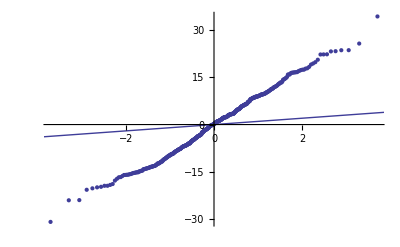

```mathematica
A=Sort[RandomReal[NormalDistribution[0,10],500]];A=Table[{Quantile[StudentTDistribution[10]//N,i/(Length[A]+1)],A[[i]]},{i,Length[A]}];Show[ListPlot[A],Plot[x,{x,A[[1,2]],A[[Length[A],2]]}]]
```